# Team 2 Sean Link Jinsung Lee Parker Hailberg ES204-PC01 Project 3

## Equation and Variable Definition

Equations
    LagrangianS = Lagrangian of the entire system
    Lagrangianhc = Lagrangian of the half cylinder
    LagrangianDisk = Lagrangian of the disk
Variables
    M = mass of the half cylinder (kg)
    R = radious of the half cylinder (m)
    Izcmhc = Moment of inertia of the half cylinder about its center of mass (kg m^2)
    Vcmhc = velocity of the center of mass of the half cylinder
    θ [t] = angular displacement of the half cylinder (rad)
    θ’[t] = angular velocity of the half cylinder (rad/s)
    g = acceleration due to gravity (m/s^2)
    m = mass of the disk (kg)
    VcmDisk = velocity of the center of mass of the disk (m/s)
    IzcmDisk = moment of inertia of the disk about its center of mass (kg m^2)
    wd = rotiational velocity of the disk (rad/s)
    r = radious of the disk (m)
    ϕ [t] = angular displacement of the disk relative to the contact point between the half cylinder and the ground (rad)
    ϕ’[t] = rate of change of the angular displacement of the half cylinder with respect to time (rad/s)

## Part 1: storing moment of inertia of the half cylinder about its center of mass

```mathematica
Izcmhc=M R^2(1-4/π^2);
```

## Part 2: Lagrangian of Half Cylinder

```mathematica
Lagrangianhc = 1/2 M Vcmhc^2+1/2 Izcmhc*(θ'[t])^2-M g R (1-2/π Cos[θ[t]]);
```

### Storing velocity of the center of mass of the half cylindar

```mathematica
Vcmhc = √((θ'[t] R  2/π Cos[θ[t]]-θ'[t] R)^2+(θ'[t] R 2/π Sin[θ[t]])^2);
```

### Displaying Lagrangianhc

```mathematica
Simplify[Lagrangianhc]//TraditionalForm
```

(M R (π-2 cos(θ(t))) (R (θ'(t))^2-g))/π

## Part 3: Lagrangian of the Disk

```mathematica
LagrangianDisk = 1/2 m VcmDisk^2+1/2 IzcmDisk wd^2-m g (R-(R-r)Cos[ϕ[t]]);
```

### storing wd in terms of knowns

```mathematica
wd = (θ'[t] R+r ϕ'[t]-R ϕ'[t])/r;
```

### storing VcmDisk in terms of knows

```mathematica
VcmDisk = √(((R-r)ϕ'[t] Cos[ϕ[t]]-θ'[t]R)^2+((R-r)ϕ'[t]Sin[ϕ[t]])^2);
```

### storing IzcmDisk in terms of knowns

```mathematica
IzcmDisk = 1/2 m r^2;
```

### Displaying Lagrangian of the Disk

```mathematica
Simplify[LagrangianDisk]//TraditionalForm
```

1/4 m (-4 g ((r-R) cos(ϕ(t))+R)+((r-R) ϕ'(t)+R θ'(t))^2+2 (((r-R) ϕ'(t) cos(ϕ(t))+R θ'(t))^2+(r-R)^2 (ϕ'(t))^2 sin^2(ϕ(t))))

## Creating new equation for the Lagrangian of the system

```mathematica
LagrangianS = LagrangianDisk+Lagrangianhc;
```

## Part 4: Finding Equations of motion

```mathematica
equation1=D[D[LagrangianS,θ'[t]],t]-D[LagrangianS,θ[t]]==0;
```

```mathematica
equation2 = D[D[LagrangianS,ϕ'[t]],t]-D[LagrangianS,ϕ[t]]==0;
```

```mathematica
EOMs = Solve[{equation1,equation2},{θ''[t],ϕ''[t]}]//Simplify
```

{{θ''[t]→(g (6 M Sin[θ[t]]+m π (Sin[ϕ[t]]+Sin[2 ϕ[t]]))+6 M R Sin[θ[t]] θ'[t]^2-3 m π (r-R) Sin[ϕ[t]] ϕ'[t]^2)/(R (12 M Cos[θ[t]]+π (-3 m-6 M+2 m Cos[ϕ[t]]+m Cos[2 ϕ[t]]))),ϕ''[t]→-((g (2 M (1+2 Cos[ϕ[t]]) Sin[θ[t]]+(3 m π+4 M π-8 M Cos[θ[t]]) Sin[ϕ[t]])+2 M R (1+2 Cos[ϕ[t]]) Sin[θ[t]] θ'[t]^2-m π (r-R) (Sin[ϕ[t]]+Sin[2 ϕ[t]]) ϕ'[t]^2)/((r-R) (12 M Cos[θ[t]]+π (-3 m-6 M+2 m Cos[ϕ[t]]+m Cos[2 ϕ[t]]))))}}

## Part 5: Finding EOM such that the disk does not exist

substituting m = 0 in original equation θ^(..)

```mathematica
EOMs[[1]][[1]]/.m->0//Simplify
```

θ''[t]→(Sin[θ[t]] (g+R θ'[t]^2))/(R (-π+2 Cos[θ[t]]))

Note: Analytical work matches this equation

## Part 6: Finding EOM such that the half cylinder is fixed

```mathematica
Solve[D[D[LagrangianDisk,ϕ'[t]],t]-D[LagrangianDisk,ϕ[t]]==0,ϕ''[t]]/.{θ'[t]->0,θ''[t]->0}//Simplify
```

{{ϕ''[t]→(2 g Sin[ϕ[t]])/(3 r-3 R)}}

Note: Analytical work matches this equation

Note: Numberical approximations to find the peroid of the two equations in Part 5 and Part 6 are done in MATLAB

## Part 7: Integrating and plotting equations of motion

### Initializing Constants

```mathematica
M = 0.578;(*kg*)
m = 0.162;(*kg*)
R = 0.15625;(*m*)
r = 0.038;(*m*)
g = 9.81;(*m/s^2*)
```

### Plotting EOMs with following initial conditions

θ(0) = 0, θ̇(0)=0, ϕ(0) = π/18, ϕ̇(0) = 0

```mathematica
solutionCurves1 =NDSolveValue[{equation1,equation2,θ[0]==0,θ'[0]==0,ϕ[0]==π/18,ϕ'[0]==0},{θ,ϕ},{t,0,6}];
```

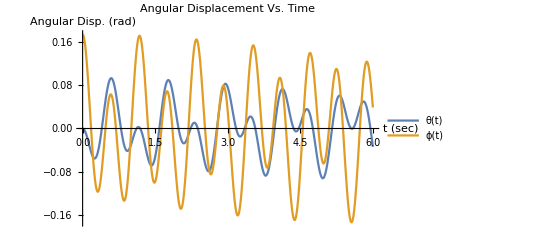

```mathematica
Plot[{solutionCurves1[[1]][t],solutionCurves1[[2]][t]},{t,0,6},PlotLabel->"Angular Displacement Vs. Time",
AxesLabel->{"t (sec)", "Angular Disp. (rad)"},PlotLegends->{"θ(t)","ϕ(t)"}]
```

### Plotting EOMs with following initial conditions

θ(0) = π/18, θ̇(0)=0, ϕ(0) = π/9, ϕ̇(0) = 0

```mathematica
solutionCurves2 =NDSolveValue[{equation1,equation2,θ[0]==π/18,θ'[0]==0,ϕ[0]==π/9,ϕ'[0]==0},{θ,ϕ},{t,0,6}];
```

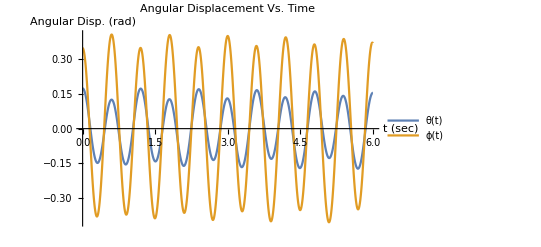

```mathematica
Plot[{solutionCurves2[[1]][t],solutionCurves2[[2]][t]},{t,0,6},PlotLabel->"Angular Displacement Vs. Time",
AxesLabel->{"t (sec)", "Angular Disp. (rad)"},PlotLegends->{"θ(t)","ϕ(t)"}]
```

### Plotting EOMs with following initial conditions

θ(0) = π/9, θ̇(0)=0, ϕ(0) = -π/9, ϕ̇(0) = 0

```mathematica
solutionCurves3=NDSolveValue[{equation1,equation2,θ[0]==π/9,θ'[0]==0,ϕ[0]==-π/9,ϕ'[0]==0},{θ,ϕ},{t,0,6}];
```

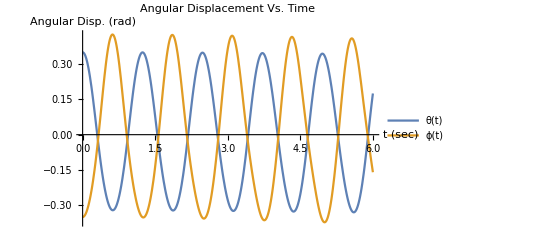

```mathematica
Plot[{solutionCurves3[[1]][t],solutionCurves3[[2]][t]},{t,0,6},PlotLabel->"Angular Displacement Vs. Time",
AxesLabel->{"t (sec)", "Angular Disp. (rad)"},PlotLegends->{"θ(t)","ϕ(t)"}]
```